```mathematica
Clear["Global`*"];
(*龙本身的运动损耗与温度的关系*)
data1={{-50,5},{0,1.3},{10,1}};
f1=Fit[data1,{1,x,x^2,x^3},x];
data2={{30,1},{40,1.4},{50,2}};
f2=Fit[data2,{1,x,x^2,x^3},x];
m[x_]=Piecewise[{{f1,-50<=x<10},{1,10≤x≤30},{f2,30<x<=50}}];
Plot[m[x],{x,-50,50}];
(*湿度对龙的效率的影响*)data={{55,1},{60,1.2},{65,1.4},{70,1.7},{52,0.9},{48,0.8},{40,0.85},{35,0.93},{30,1.1},{25,1.5}};
f=Fit[data,{1,y,y^2,y^3},y];
draeff[x_,y_]=f*m[x];
Plot3D[draeff[x,y],{x,-50,50},{y,25,70}];
(*食物密度随着温度的变化*)
data1={{-55,0},{-60,0},{-50,0},{-45,0.0001},{-40,0.005},{-30,0.01},{-20,0.05},{-10,0.1},{0,0.3},{5,0.5},{10,0.6},{16,0.86},{18,0.95},{19,0.98},{20,1},{21,0.99},{22,0.97},{23,0.95},{27,0.8},{30,0.7},{35,0.5},{40,0.3},{50,0.03},{60,0.01},{65,0},{70,0}};

fT=Interpolation[data1];
Plot[fT[x],{x,-50,50}];
gT[x_]=1/√fT[x];
(*食物密度随着湿度的变化*)data={{55,1},{60,0.9},{63,0.75},{66,0.63},{70,0.5},{75,0.3},{53,0.95},{50,0.84},{46,0.72},{40,0.6},{30,0.4},{25,0.3}};

fH=Fit[data,{1,y,y^2,y^3},y];
gH=1/√fH;
ρ[x_,y_]=fT[x]*fH;
Plot3D[ρ[x,y],{x,-50,50},{y,25,70}];
food[x_,y_]=gT[x]*gH;
fincost[x_,y_]=draeff[x,y]*food[x,y];(*龙捕食相同量的食物受到的温度和湿度的双重影响*)
(*注意：x代表温度，y代表湿度*)
Plot[{f,gH},{y,25,70},Frame->{{True,True},{True,False}},FrameTicks->{{{1,1.5},{1,1.5}},{Automatic,None}},FrameLabel->{{"Dragon","food"},{"Humidity",None}},PlotLegends->{"Dragon's metabolic rate","unit cost for seeking food"}];
(*迁徙路线的温度分布图*)
data={{0,26},{213,33},{693,45},{1173,50},{1653,38},{1893,26},{2373,20},{2613,18},{3093,16},{3453,15},{3573,13},{4053,10},{4533,0},{5013,-10},{5483,-25}};(*0处是阳戬城，1893处为河湾地腹地,3093处为河间地腹地,4053开始进入北境*)
disandtem=Fit[data,{1,x,x^2,x^3,x^4,x^5},x];
graph1=Plot[disandtem,{x,0,5483},PlotRange->{{-1000,Automatic},{-30,50}},Ticks->{{0,1173,1893,3093,4053,5483,2373,3453},{0,26,50,16,10,-25}},AxesLabel->{"Position","Temperature"},AxesOrigin->{0,0}, ImageSize->Large,Epilog->{Line[{{1173,44},{1173,0}}],Line[{{2373,0},{2373,22}}],Line[{{3453,0},{3453,13}}],Line[{{4053,0},{4053,8.7}}]}];

(*湿度和位置的关系*)
data={{0,50},{213,35},{693,25},{1173,30},{1653,46},{1893,60},{2373,56},{2613,53},{3093,55},{3453,63},{3573,70},{4053,60},{4533,45},{5013,37},{5483,33}};(*0处是阳戬城，1893处为河湾地腹地,3093处为河间地腹地,4053开始进入北境*)

disandhum=Interpolation[data,InterpolationOrder->3];
graph1=Plot[disandhum[x],{x,0,5483},Ticks->{{0,1173,1893,3093,4053,5483,2373,3453},{50,25,60,70,33}},AxesLabel->{"Position","Humidity"},AxesOrigin->{0,0}, ImageSize->Large,Epilog->{Line[{{1173,30},{1173,0}}],Line[{{2373,0},{2373,56}}],Line[{{3453,0},{3453,63}}],Line[{{4053,0},{4053,60}}]},PlotRange->{Automatic,{0,80}}];
(*最后的只关于位置的函数*)
H[x_]=ρ[disandtem,disandhum[x]];
eff[x]=fincost[disandtem,disandhum[x]];
Plot[H[x],{x,0,5483},AxesLabel->{"position","food's quantity"}];
Plot[eff[x],{x,0,5483},AxesLabel->{"position","efficient"}];
effdata=Table[eff[x]/.x->240*i,{i,0,22}];
hdata=Table[H[i*240],{i,0,22}];
effdata=Table[eff[x]/.x->240*i,{i,0,22}];
hdata=Table[H[i*240],{i,0,22}];
m={1};
Do[AppendTo[m,m[[i]]+200*(1.4(m[[i]])^0.6/(100+50/((hdata[[i]])^2(0.0375)^2))-effdata[[i]]/(185*10^3)1.4*(m[[i]])^1.6)],{i,1,22}];
xf=Table[{240*(i-1),m[[i]]},{i,1,22}];
xffinal=Interpolation[xf];
Plot[xffinal[x],{x,0,5483},Epilog->{Line[{{1173,xffinal[1173]},{1173,0}}],Line[{{2373,0},{2373,xffinal[2373]}}],Line[{{3453,0},{3453,xffinal[3453]}}],Line[{{4053,0},{4053,xffinal[4053]}}],Text[NumberForm[xffinal[1173],3],{1173,xffinal[1173]+0.005}],Text[NumberForm[xffinal[2373],3],{2373,xffinal[2373]+0.005}],Text[NumberForm[xffinal[3453],3],{3453,xffinal[3453]+0.005}],Text[NumberForm[xffinal[4053],3],{4053+100,xffinal[4053]+0.005}],Text[NumberForm[xffinal[5483],3],{5483-150,xffinal[5483]+0.01}]},PlotRange->{Automatic,{0.9,1.1}},Ticks->{{1173,2373,3453,4053,5483},{1}},AxesLabel->{"position","Mass's relative value"}];
```

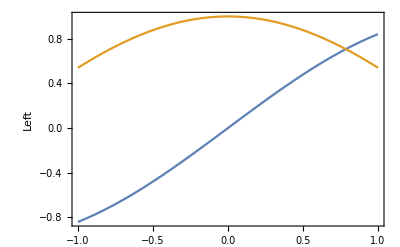

InterpolatingFunction[…]

```mathematica
Plot[{Sin[x],Cos[x]},{x,-1,1},Frame->{{True,True},{True,False}},FrameTicks->{{Automatic,{{-0.5,5},{0,10},{0.5,15}}},{Automatic,None}},FrameLabel->{{"Left","Right"},{None,None}}]
```

```mathematica
Plot3D[pco[x,y],{x,0,2500},{y,0,5483},Mesh->None,AxesLabel->{"time","position","Mass"}]
```

InterpolatingFunction::dmval: 输入值 {0.17875,0.392035} 位于插值函数的数据范围之外. 将使用外推法.

-Graphics3D-

```mathematica
py={};
dt=50;
m={1};
Do[

AppendTo[m,m[[j]]+dt hdata[[10]](m[[j]]^0.6-1/(185*10^4)m[[j]]^1.6)],{j,1,1000,1}];
m;
mx=Table[{(i-1)*dt,m[[i]]},{i,1,1000}];
mxo=Interpolation[mx]
g1=Plot[mxo[x],{x,0,50000},AxesLabel->{"time","mass"},PlotLegends->{"The Reach"},PlotStyle->Blue];
py={};
dt=50;
m={1};
Do[

AppendTo[m,m[[j]]+dt hdata[[2]](m[[j]]^0.6-1/(185*10^4)m[[j]]^1.6)],{j,1,1000,1}];
m;
mx=Table[{(i-1)*dt,m[[i]]},{i,1,1000}];
mxo=Interpolation[mx]
g2=Plot[mxo[x],{x,0,50000},AxesLabel->{"time","mass"},PlotLegends->{"Dorne's desert"},PlotStyle->Green];
py={};
dt=50;
m={1};
Do[

AppendTo[m,m[[j]]+dt hdata[[22]](m[[j]]^0.6-1/(185*10^4)m[[j]]^1.6)],{j,1,1000,1}];
m;
mx=Table[{(i-1)*dt,m[[i]]},{i,1,1000}];
mxo=Interpolation[mx]
g3=Plot[mxo[x],{x,0,50000},AxesLabel->{"time","mass"},PlotLegends->{"The Wall"},PlotStyle->Red]


(*py={};
dt=50;
Do[m={1};
Do[

AppendTo[m,m[[j]]+dt hdata[[i]](m[[j]]^0.6-1/(185*10^3)m[[j]]^1.6)],{j,1,50,1}];AppendTo[py,m],{i,1,22}];  
pc=Flatten[Table[Table[{{i*240,j*dt},py[[i,j]]},{j,1,50}],{i,1,22}],1];
pco=Interpolation[pc];
Plot3D[pco[x,y],{x,0,1000},{y,0,5483},Mesh->None,ColorFunction->"Rainbow",AxesLabel->{"Position","Time","Mass"},PlotRange->{Automatic,Automatic,{0,Infinity}}]*)

Show[{g1,g3}]
```